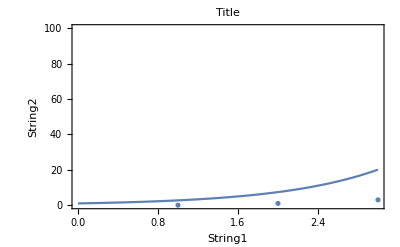

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week4/quiz/"];
res = ReadList["!./a.out",{Number,Number}(*Number, Number,...*) ];
x1 = 0;
x2 = 3;
y1 = 0;
y2 = 100;
xlabel = "String1";
ylabel = "String2";
title = "Title";
simplelistplot = ListPlot[res, Frame->True, PlotRange->{{x1, x2}, {y1,y2}},FrameLabel->{xlabel, ylabel}];
simpleplot = Plot[Exp[x],{x,0,3},PlotRange-> {{x1,x2},{y1,y2}}];
Show[simplelistplot, simpleplot, PlotLabel-> title]
```

```mathematica
datac = ReadList["data.txt",{Number, Number}(*Number, Number,...*) ]
```

{{1,1},{2,3},{3,6},{4,10},{5,15},{6,21},{7,28},{8,36},{9,45},{10,55},{11,66},{12,78},{13,91},{14,105},{15,120},{16,136},{17,153},{18,171},{19,190},{20,210},{21,231},{22,253},{23,276},{24,300},{25,325},{26,351},{27,378},{28,406},{29,435},{30,465},{31,496},{32,528},{33,561},{34,595},{35,630},{36,666},{37,703},{38,741},{39,780},{40,820},{41,861},{42,903},{43,946},{44,990},{45,1035},{46,1081},{47,1128},{48,1176},{49,1225},{50,1275},{51,1326},{52,1378},{53,1431},{54,1485},{55,1540},{56,1596},{57,1653},{58,1711},{59,1770},{60,1830},{61,1891},{62,1953},{63,2016},{64,2080},{65,2145},{66,2211},{67,2278},{68,2346},{69,2415},{70,2485},{71,2556},{72,2628},{73,2701},{74,2775},{75,2850},{76,2926},{77,3003},{78,3081},{79,3160},{80,3240},{81,3321},{82,3403},{83,3486},{84,3570},{85,3655},{86,3741},{87,3828},{88,3916},{89,4005},{90,4095},{91,4186},{92,4278},{93,4371},{94,4465},{95,4560},{96,4656},{97,4753},{98,4851},{99,4950},{100,5050}}

```mathematica
u
```

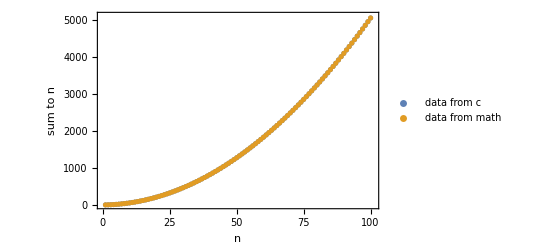

```mathematica
ListPlot[{datac,datam}, Frame->True, PlotRange->{{0,101}, {0,5100}}, FrameLabel->{"n", "sum to n"}, PlotLegends->{"data from c", "data from math"}]
```

```mathematica
Table[{i, i(i+1)/2}, {0<i<100}]
```

Table::iterb: Iterator {0<i<100} does not have appropriate bounds.

```mathematica
datam = Table[{i,1/2 i (i+1)},{i,100}]
```

{{1,1},{2,3},{3,6},{4,10},{5,15},{6,21},{7,28},{8,36},{9,45},{10,55},{11,66},{12,78},{13,91},{14,105},{15,120},{16,136},{17,153},{18,171},{19,190},{20,210},{21,231},{22,253},{23,276},{24,300},{25,325},{26,351},{27,378},{28,406},{29,435},{30,465},{31,496},{32,528},{33,561},{34,595},{35,630},{36,666},{37,703},{38,741},{39,780},{40,820},{41,861},{42,903},{43,946},{44,990},{45,1035},{46,1081},{47,1128},{48,1176},{49,1225},{50,1275},{51,1326},{52,1378},{53,1431},{54,1485},{55,1540},{56,1596},{57,1653},{58,1711},{59,1770},{60,1830},{61,1891},{62,1953},{63,2016},{64,2080},{65,2145},{66,2211},{67,2278},{68,2346},{69,2415},{70,2485},{71,2556},{72,2628},{73,2701},{74,2775},{75,2850},{76,2926},{77,3003},{78,3081},{79,3160},{80,3240},{81,3321},{82,3403},{83,3486},{84,3570},{85,3655},{86,3741},{87,3828},{88,3916},{89,4005},{90,4095},{91,4186},{92,4278},{93,4371},{94,4465},{95,4560},{96,4656},{97,4753},{98,4851},{99,4950},{100,5050}}